```mathematica
SetDirectory["C:\\Users\\pglpm\\repositories\\genobayes\\scripts2\\"]
```

C:\Users\pglpm\repositories\genobayes\scripts2

```mathematica
bd[x_,a_,b_]=PDF[BetaDistribution[b,a],x]
```

Piecewise[{{((1-x)^(-1+a) x^(-1+b))/Beta[b,a], 0<x<1}, {0, True}}]

```mathematica
cd[x_]=Assuming[x>0,FS@Log[PDF[CauchyDistribution[Log[1000],Log[1000]],x]]]
```

-Log[π (x^2-6 x Log[10]+18 Log[10]^2)]+Log[Log[1000]]

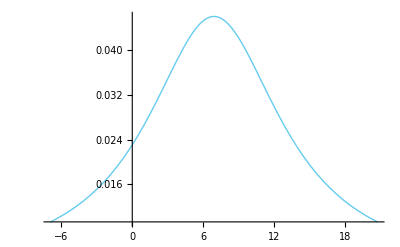

```mathematica
Plot[Exp[cd[lx]],{lx,Log[10^-3],Log[10^9]},PlotRange->Auto]
```

```mathematica
data=Import["dataset1_binarized.csv"][[2;;,2;;]];
savedir="1gene-results_math7\\";
filename="gene";
allgenes=Range[1,94];
allsymptoms=Range[1,3];
symptomnames={"A","B","C"};
quantiles={0.05,0.95};
```

```mathematica
alnames={"0","1"};
gnames=Import["dataset1_binarized.csv"][[1,4+allgenes]];

qnames={"EV","STD","Q.05","Q.95","theta0","theta1","post.theta0","post.theta1"};
```

```mathematica
binoutcomes={0,1};
noutcomes=Length@binoutcomes;
alcombnames=alnames;
nalleles=Length@alnames;
ncombinations=Length@allgenes;
```

```mathematica
i=1;sdata=data[[;;,Join[{i},3+allgenes]]];
```

```mathematica
g1=10;f=Table[Count[Select[sdata,(#[[1+g1]]==x)&][[;;,1]],al],{al,{0,1}}
,{x,binoutcomes}]
```

{{1769,2599},{666,995}}

```mathematica
logprob[t_]:=Block[{r2=f+t},
Total@Flatten@LogGamma[r2]-
Total@LogGamma[Total@r2]+
noutcomes*(LogGamma[Total@t]-Total@LogGamma[t])
(*-2*Log[Total@t] (*math3*) *)
(*-Total@Log[t](*math4*)*)
(*+cd[Log[Total@t]]-2*Log[Total@t] (*math5*)*)
(* nothing: math6 *)
(*+Total@cd2[t] (*math7*)*)
+Total[cd[Log[t]]-Log[t]]
];
```

```mathematica
logprob[Range[2]]//N
```

-3566.05

```mathematica
thetas2=thetas[[;;2]]
```

{t$1,t$2}

```mathematica
FindMaximum[{logprob[thetas2],Sequence@@((#>0)&/@thetas2)},T[{thetas2,Mean[f]}]]
```

{-3563.37,{t$1→0.124409,t$2→0.103179}}

```mathematica
NIntegrate[Evaluate[thetas*Exp[logprob[thetas]]*Exp[3563]],Evaluate[Sequence@@Table[{xx,0,+Infinity},{xx,thetas}]]]/NIntegrate[Evaluate[Exp[logprob[thetas]]*Exp[3563]],Evaluate[Sequence@@Table[{xx,0,+Infinity},{xx,thetas}]]]
```

{0.000872723 NIntegrate[(ⅇ^(3563+LogGamma[1958+t$1]+LogGamma[2410+t$1]+LogGamma[740+t$2]+LogGamma[921+t$2]+2 (-LogGamma[t$1]-LogGamma[t$2]+LogGamma[t$1+t$2])-LogGamma[2698+t$1+t$2]-LogGamma[3331+t$1+t$2]) Log[1000]^2)/(π^2 t$2 (18 Log[10]^2-6 Log[10] Log[t$1]+Log[t$1]^2) (18 Log[10]^2-6 Log[10] Log[t$2]+Log[t$2]^2)),{t$1,0,∞},{t$2,0,∞}],0.000872723 NIntegrate[(ⅇ^(3563+LogGamma[1958+t$1]+LogGamma[2410+t$1]+LogGamma[740+t$2]+LogGamma[921+t$2]+2 (-LogGamma[t$1]-LogGamma[t$2]+LogGamma[t$1+t$2])-LogGamma[2698+t$1+t$2]-LogGamma[3331+t$1+t$2]) Log[1000]^2)/(π^2 t$1 (18 Log[10]^2-6 Log[10] Log[t$1]+Log[t$1]^2) (18 Log[10]^2-6 Log[10] Log[t$2]+Log[t$2]^2)),{t$1,0,∞},{t$2,0,∞}]}

```mathematica
logprob[{1,2}]//N
```

-3562.38

```mathematica
(* Calculate posterior theta parameters and resulting standard deviations and quantiles *)

Do[(*Print[i];*)
sdata=data[[;;,Join[{i},3+allgenes]]];

Do[ClearAll[logprob];
f=Table[Count[Select[sdata,(#[[1+g1]]==x)&][[;;,1]],al],{al,{0,1}}
,{x,binoutcomes}];

logprob[t_]:=Block[{r2=f+t},
Total@Flatten@LogGamma[r2]-
Total@LogGamma[Total@r2]+
noutcomes*(LogGamma[Total@t]-Total@LogGamma[t])
(*-2*Log[Total@t] (*math3*) *)
(*-Total@Log[t](*math4*)*)
(*+cd[Log[Total@t]]-2*Log[Total@t] (*math5*)*)
(* nothing: math6 *)
(*+Total@cd2[t] (*math7*)*)
+Total[cd[Log[t]]-Log[t]]
];

theta={x,y}/.FindMaximum[{logprob[{x,y}],x>0,y>0},{{x,1},{y,1}}][[2]];

fnew=f+theta;
nnew=Total@fnew;
quantities={
(* EV *)
Flatten[T[T[fnew[[2;;]]]/nnew],1],
(* STD *)
Sqrt[(Times@@fnew)/(nnew^2*(1+nnew))],
(* Quantiles *)
Sequence@@(T@Table[Quantile[BetaDistribution[Sequence@@(Reverse[fnew[[;;,al]]])],quantiles],{al,binoutcomes+1}]),
(* Theta *)
Sequence@@(T@Table[theta,noutcomes]),
(* f + theta *)
Sequence@@fnew
};

csvquantities=Join[{Prepend[alnames,""]},T[Join[{qnames},T@quantities]]];

Export[savedir<>filename<>ToString[g1]<>"_s"<>symptomnames[[i]]<>".csv",csvquantities]
,{g1,allgenes}]
,{i,allsymptoms}]
```

```mathematica
(* Calculate various measures of "spread" *)

Do[(*Print[i];*)
(*meanf=Mean[data[[;;,i]]];*)
spread=
Table[
values=Import[savedir<>filename<>ToString[g1]<>"_s"<>symptomnames[[i]]<>".csv"][[2;;3,2;;]];
(*values=resu[[1]];*)
sp=Max[Abs@Differences[values[[1]]]/Total[values[[2]]]];
(*fmax=Max[values];
fmin=Min[values];drms=Sqrt[Mean[(values-meanf)^2]];
arms=Abs@Differences[values][[1]] *)(* only works for two-valued case *);
{g1,sp}
,{g1,allgenes}];
Export["diffmeasures7_1gene_s"<>symptomnames[[i]]<>".csv",Join[{{"SNP","norm.spread"}},spread]];

,{i,allsymptoms}]
```

```mathematica
(* Make plots for alleles sorted by different measures of spread *)
```

```mathematica
datadir="1gene-results_math7\\";data2[sy_,g1_]:=T[Import[datadir<>"gene"<>ToString[g1]<>"_s"<>symptomnames[[sy]]<>".csv"][[2;;,2;;]]];
```

```mathematica
ClearAll[spreads];
(*spreads[sy_]:=(thespread=Import["diffmeasures2_1gene_s"<>symptomnames[[sy]]<>".csv"][[2;;,;;]];
thespread[[;;,3]]=-thespread[[;;,3]];
spreads[sy]=thespread);*)

spreads[sy_]:=Import["diffmeasures7_1gene_s"<>symptomnames[[sy]]<>".csv"][[2;;,;;]];
```

```mathematica
Needs["ErrorBarPlots`"];
```

```mathematica
geneseq=Import["dataset1_binarized.csv"][[1,5;;]];
geneseq=Table[ToString[i]<>" "<>geneseq[[i]],{i,Length@geneseq}];
```

```mathematica
numpairs=Length@allgenes;
sortcolumn=2 (* 1: no sort, 2: normalized spread *);
columnnames={"normspread"};
Do[
sortspreads=Sort[spreads[sym],(#1[[sortcolumn]]>#2[[sortcolumn]])&][[;;,1]];
data=Flatten[Table[data2[sym,Sequence@@sortspreads[[ii]]][[;;,1;;2]],{ii,numpairs}],1];

min=Min[data[[;;,1]]-data[[;;,2]]];
max=Max[data[[;;,1]]+data[[;;,2]]];

ticknames=Flatten@Table[{geneseq[[sortspreads[[ii]]]]<>"        "<>alnames[[1]],"        "<>alnames[[2]]},{ii,numpairs}];

plot=ErrorListPlot[data[[;;,{1,2}]],Joined->False,PlotRange->{min,max},Joined->False,AspectRatio->1/7,Frame->Auto,Axes->None,FrameLabel->{Style["SNP",41],Style[freq["symptom | SNP allele"],41]},
FrameStyle->Directive[Large,Black],
FrameTicks->{Auto,{T@{Range[numpairs*nalleles],Style[#,15]&/@(Rotate[#,Pi/2]&/@(ticknames))},None}},
PlotStyle->PointSize[Scaled[0.005]],GridLines->{
Table[{i,Thick},{i,1/2,numpairs*nalleles+1/2,nalleles}]
,Auto},ImageSize->a4longside*{5.5,1},Epilog->Text[Style["symptom "<>symptomnames[[sym]],42],Sequence@@labelposition[{0.5,0.99}]]];
Export["sort7"<>If[sortcolumn>1,"_"<>columnnames[[sortcolumn-1]],""]<>"_1gene_std_s"<>symptomnames[[sym]]<>".pdf",plot];
,{sym,3},{sortcolumn,{2}}]
```

```mathematica
resu=Import[savedir<>filename<>ToString[6]<>"_s"<>symptomnames[[1]]<>".csv"][[2;;,2;;]]
```

```mathematica
resu={{0.259170041293112,0.2835056871550766},{0.008047270661176678,0.006356164161544898},{0.24602617884103603,0.273099777196446},{0.27249871224939903,0.29400954440503735},{714.7260245717754,714.7260245717754},{266.147127108531,266.147127108531},{2195.7260245717753,3601.7260245717753},{768.147127108531,1425.147127108531}}
```

{{0.25917,0.283506},{0.00804727,0.00635616},{0.246026,0.2731},{0.272499,0.29401},{714.726,714.726},{266.147,266.147},{2195.73,3601.73},{768.147,1425.15}}

```mathematica
%//MF
```

(0.25917 | 0.283506
0.00804727 | 0.00635616
0.246026 | 0.2731
0.272499 | 0.29401
714.726 | 714.726
266.147 | 266.147
2195.73 | 3601.73
768.147 | 1425.15)

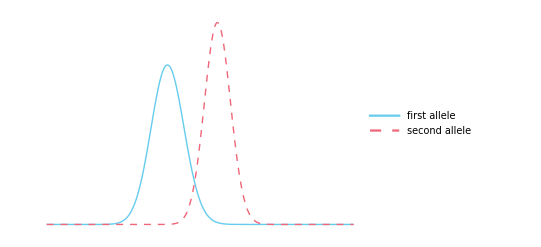

```mathematica
Plot[{bd[x,Sequence@@resu[[7;;8,1]]],bd[x,Sequence@@resu[[7;;8,2]]]},{x,0.2,0.35},PlotRange->All,Axes->None,Frame->Auto,FrameStyle->Directive[Large,Black],ImageSize->a5rsize,FrameLabel->{"conditional frequency symptom " S,"p"["frequency | data"]},PlotLegends->Placed[{"first allele","second allele"},labelposition[{0.05,0.9}]]]
```

```mathematica
Export["example_distr_condfreqs.pdf",%]
```

example_distr_condfreqs.pdf

```mathematica
Expectation[x,x\[Distributed] BetaDistribution[Sequence@@Reverse@#]]&/@{resu[[7;;8,1]],resu[[7;;8,2]]}
```

{0.25917,0.283506}

```mathematica
Sqrt[CentralMoment[ BetaDistribution[Sequence@@Reverse@#],2]&/@{resu[[7;;8,1]],resu[[7;;8,2]]}]
```

{0.00804727,0.00635616}

```mathematica
Variance[x,x\[Distributed] BetaDistribution[Sequence@@#]]&/@{resu[[7;;8,1]],resu[[7;;8,2]]}
```

```mathematica
del=0.01;Total@Table[NIntegrate[bd[x,Sequence@@resu[[7;;8,1]]],{x,i,i+del}]*NIntegrate[bd[x,Sequence@@resu[[7;;8,2]]],{x,i,i+del}],{i,0,1-del,del}]
```

0.0321908

```mathematica
del=0.01;NIntegrate[bd[x,Sequence@@resu[[7;;8,1]]]*bd[y,Sequence@@resu[[7;;8,2]]],{x,0,1},{y,Max[0,x-del/2],Min[1,x+del/2]}]
```

0.0278337

```mathematica
checkdata=Flatten[Table[
theta=newtheta[gx,ax];tot=Total@theta;
{theta[[2]]/tot,Sqrt[(Times@@theta)/(tot^2*(1+tot))]},{gx,1,checkgenes},{ax,0,1}],1];
```

```mathematica
checkgenes=94;geneseq=Import["allcondfreqs_1gene_thetamax_sA.csv"][[1,2;;checkgenes*2+1]];
geneseq=Table[ToString[Ceiling[i/2]]<>" "<>geneseq[[i]],{i,Length@geneseq}];

symptomnames={"A","B","C"};allelenames={"A","B"};
```

```mathematica
(* save seq of results *)
ClearAll[checkdata2];
ii=0;Do[Print[sym];ii=ii+1;
datacf=T[Import["condcounts_s"<>sym<>".csv"][[2;;,2;;]]];

ClearAll[logprob,newtheta];
logprob[t_,g_]:=Block[{r2=g+t},
Total@Flatten@LogGamma[r2]-
Total@LogGamma[Total@r2]+
(Length@T@r2)*(LogGamma[Total@t]-Total@LogGamma[t])];

newtheta[g_]:=Block[{fm,dat=datacf[[;;,{2*g-1,2*g}]]},
fm=({x,y}/.FindMaximum[{logprob[{x,y},dat],x>0,y>0},{{x,1},{y,1}}][[2]]);
Table[dat[[;;,ax]]+fm,{ax,2}]];

checkdata2[ii]=Table[
theta=newtheta[gx][[ax]];tot=Total@theta;
{theta[[2]]/tot,Sqrt[(Times@@theta)/(tot^2*(1+tot))]},{gx,1,checkgenes},{ax,2}];
,{sym,symptomnames}]
```

```mathematica
Dimensions[checkdata2[1]]
```

{94,2,2}

```mathematica
checkdata2[1][[3]]
```

{{0.275632,0.00127375},{0.275273,0.00128111}}

```mathematica
checkdata[1][[;;10]]
```

{{0.270465,0.00582025},{0.290821,0.00861374},{0.275452,0.00171662},{0.27555,0.00170884},{0.275632,0.00127375},{0.275273,0.00128111},{0.275645,0.00175302},{0.275373,0.00175147},{0.275478,0.000943611},{0.275652,0.00095159}}

```mathematica
min=Min[checkdata[[;;,1]]-checkdata[[;;,2]]];
max=Max[checkdata[[;;,1]]+checkdata[[;;,2]]];
```

```mathematica
Needs["ErrorBarPlots`"];
```

```mathematica
ii=0;Do[Print[sym];ii=ii+1;

min=Min[Flatten[checkdata2[ii],1][[;;,1]]-Flatten[checkdata2[ii],1][[;;,2]]];
max=Max[Flatten[checkdata2[ii],1][[;;,1]]+Flatten[checkdata2[ii],1][[;;,2]]];

sortdata=SortBy[


checkdata[ii]=Table[
theta=newtheta[gx,ax];tot=Total@theta;
{theta[[2]]/tot,Sqrt[(Times@@theta)/(tot^2*(1+tot))]},{gx,1,checkgenes},{ax,0,1}];(*rows: genes, cols: alleles, 3rd: mean+std *)

min=Min[checkdata[[;;,1]]-checkdata[[;;,2]]];
max=Max[checkdata[[;;,1]]+checkdata[[;;,2]]];plot=ErrorListPlot[checkdata[[;;,{1,2}]],PlotRange->{min,max},Joined->False,AspectRatio->1/7,Frame->Auto,Axes->None,FrameLabel->{Style[gene,41],Style[freq[symptom|"gene allele"],41]},
FrameStyle->Directive[Large],
FrameTicks->{Auto,{T@{Range[checkgenes*2],Style[#,15]&/@(Rotate[#,Pi/2]&/@(geneseq))},None}},
PlotStyle->PointSize[Scaled[0.005]],GridLines->{Range[1/2,checkgenes*2+1/2,2],Auto},ImageSize->a4longside*{6,1},Epilog->Text[Style["symptom "<>sym,42],Sequence@@labelposition[{0.5,0.9}]]];
Export["1gene_std_s"<>sym<>".pdf",plot];,
{sym,symptomnames}]
```

```mathematica
(* with quantiles instead of std *)
Do[Print[sym];
datacf=T[Import["condcounts_s"<>sym<>".csv"][[2;;,2;;]]];
ClearAll[logprob,newtheta];
logprob[t_,g_]:=Block[{r2=datacf[[;;,{2*g-1,2*g}]]+t},
Total@Flatten@LogGamma[r2]-
Total@LogGamma[Total@r2]+
(Length@T@r2)*(LogGamma[Total@t]-Total@LogGamma[t])];

newtheta[g_,i_]:=datacf[[;;,2*g-1+i]]+({x,y}/.FindMaximum[{logprob[{x,y},g],x>0,y>0},{{x,1},{y,1}}][[2]]);

checkdata=Flatten[Table[
theta=newtheta[gx,ax];tot=Total@theta;
{{gx*2-1+ax,theta[[2]]/tot},
ErrorBar[-theta[[2]]/tot+Quantile[BetaDistribution[theta[[2]],theta[[1]]],{0.05,0.95}]]},{gx,1,checkgenes},{ax,0,1}],1];

min=Min[checkdata[[;;,1,2]]+checkdata[[;;,2,1,1]]];
max=Max[checkdata[[;;,1,2]]+checkdata[[;;,2,1,2]]];plot=ErrorListPlot[checkdata[[;;,{1,2}]],PlotRange->{min,max},Joined->False,AspectRatio->1/6,Frame->Auto,Axes->None,FrameLabel->{Style[gene,41],Style[freq[symptom|"gene allele"],41]},
FrameStyle->Directive[Large],
FrameTicks->{Auto,{T@{Range[checkgenes*2],Style[#,15]&/@(Rotate[#,Pi/2]&/@(geneseq))},None}},
PlotStyle->PointSize[Scaled[0.005]],GridLines->{Range[1/2,checkgenes*2+1/2,2],Auto},ImageSize->a4longside*{6,1},Epilog->Text[Style["symptom "<>sym,42],Sequence@@labelposition[{0.5,0.9}]]];
Export["mathematica_05quantile_s"<>sym<>".pdf",plot];,
{sym,symptomnames}]
```

```mathematica
a
```

a

```mathematica
oldtheta[3,1]
```

{1660,601}

```mathematica
newtheta[3,1]
```

{88092.5,33460.2}

```mathematica
bd[0.5,Sequence@@(newtheta[3,0])]
```

4.036684122×10^-5576

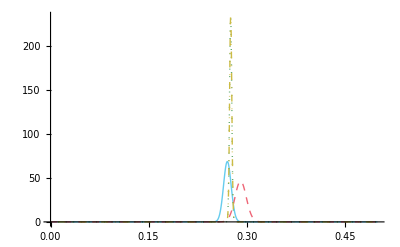

```mathematica
Plot[{bd[x,Sequence@@newtheta[1,0]],bd[x,Sequence@@newtheta[1,1]],bd[x,Sequence@@newtheta[2,0]],bd[x,Sequence@@newtheta[2,1]]},{x,0,0.5},PlotRange->All]
```